```mathematica
ClearAll["Global`*"]
```

#### code below generates the right panel in Figure 2

```mathematica
xv[τ_,tx_]:=Reap@Do[b=200; a=5*10^-7;  δ=2; d=0.25;  tl=1;T=4; σ=500; α=0.0001; 
j1[t_,tl_]:=If[0<t<tl,1/tl,0];
sol=NDSolve[{
D[s1[t], t]==s0 j1[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v2[t], t]== a b Exp[-d τ]*s1[t-τ]*v1[t-τ]-δ v2[t],
D[v1[t], t]== -δ v1[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v10,v2[t/;t≤0]==0}, 
{s1,v1,v2},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
v10 =First@Evaluate[v2[T]/.sol];
s0 = First@Evaluate[σ s1[T]/(1+ α s1[T])/.sol];
Sow[v10];
,tx];
xs[τ_,tx_]:=Reap@Do[b=200; a=5*10^-7;  δ=2; d=0.25;  tl=1;T=4; σ=500; α=0.0001;
j1[t_,tl_]:=If[0<t<tl,1/tl,0];
sol=NDSolve[{
D[s1[t], t]==s01 j1[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v2[t], t]== a b Exp[-d τ]*s1[t-τ]*v1[t-τ]-δ v2[t],
D[v1[t], t]== -δ v1[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v101,v2[t/;t≤0]==0}, 
{s1,v1,v2},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
v101 =First@Evaluate[v2[T]/.sol];
s01 = First@Evaluate[σ s1[T]/(1+ α s1[T])/.sol];
Sow[s01];
,tx];
```

```mathematica
Clear[v10,v101,s0,s01]
v10=v101=1;s0=s01=10^8;
dp2=Table[{tx,Last[Flatten[xv[2.8,tx]]],Clear[v10,v101,s0,s01];
v10=v101=1; s0=s01=10^8;},{tx,913,930,1}]/.Null->Sequence[];
```

```mathematica
discretep=Graphics[{{PointSize[0.02],Opacity[1],Point[dp2]},{Thickness[0.003],Line[dp2]}},PlotRangePadding->Scaled[.025],Frame->True,PlotRange->{{913,930},{0,2*10^8}},
FrameLabel->{Style["season",20,FontFamily->"Helvetica"],Style["parasite density",18,FontFamily->"Helvetica"]},AspectRatio->1/GoldenRatio,ImageSize->400,FrameTicksStyle->Directive[FontSize->14],FrameTicks->{{{{0,"0"},{5*10^7,"5×10^7"},{1*10^8,"1×10^8"},{1.5*10^8,"1.5×10^8"},{2*10^8,"2×10^8"}},None},{{{914,2},{916,4},{918,6},{920,8},{922,10},{924,12},{926,14},{928,16},{930,18}},None}}];
```

```mathematica
Clear[v10,v101,s0,s01]
v10=v101=1;s0=s01=10^8;
dh2=Monitor[Table[{tx,Last[Flatten[xs[2.8,tx]]],Clear[v10,v101,s0,s01];
v10=v101=1; s0=s01=10^8;},{tx,913,930,1}],tx]/.Null->Sequence[];
```

```mathematica
discreteh=Graphics[{{Gray,PointSize[0.02],Opacity[1],Point[dh2]},{Gray,Thickness[0.003],Line[dh2]}},PlotRangePadding->Scaled[.025],Frame->True,FrameLabel->{Style["",20,FontFamily->"Helvetica"],Style["host density",18,FontFamily->"Helvetica"],Style["host and parasite dynamics\n",20,FontFamily->"Helvetica"]},AspectRatio->1/GoldenRatio,PlotRange->{{913,930},{10,6.5*10^6}},ImageSize->400,FrameTicksStyle->Directive[FontSize->14],FrameTicks->{{{{0,"0"},{2*10^6,"2×10^6"},{4*10^6,"4×10^6"},{6*10^6,"6×10^6"}},None},{{{914,2},{916,4},{918,6},{920,8},{922,10},{924,12},{926,14},{928,16},{930,18}},None}}];
```

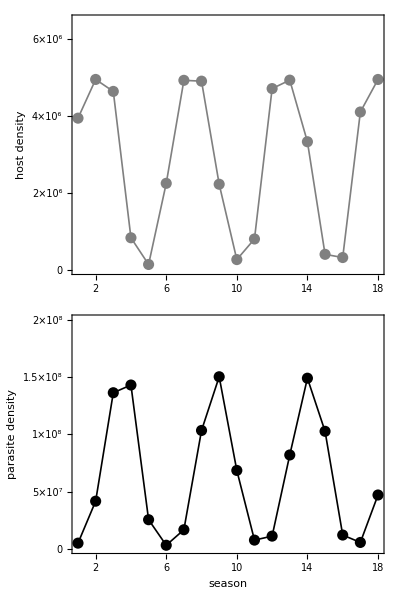

```mathematica
n3=Grid[{{discreteh},{discretep}},Spacings->0]
```

#### code below generate left panel in Figure 2

```mathematica
xb[τ_,T_,tl_]:=Reap@Do[b=200; a=3.5*10^-7;  δ=2; d=0.25;   σ=500; α=0.0001; 
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
sol=NDSolve[{
D[s1[t], t]==s0 j1[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v2[t], t]== a b Exp[-d τ]*s1[t-τ]*v1[t-τ]-δ v2[t],
D[v1[t], t]== -δ v1[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v10,v2[t/;t≤0]==0}, 
{s1,v1,v2},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
v10 =First@Evaluate[v2[T]/.sol];
s0 = First@Evaluate[σ s1[T]/(1+ α s1[T])/.sol];
Sow[v10];
,900];
```

```mathematica
Clear[v10,s0];
v10=1;s0=10^8;
list1=Monitor[Flatten[Table[{seq=Union[Flatten[xb[τx,4,1]][[800;;900]]],Clear[v10,s0];
v10=1;s0=10^8;};
Thread[{ConstantArray[τx,Length[seq]],seq}],{τx,2.4,2.8,0.001}],1],τx]
```

```mathematica
Clear[v10,s0];
v10=1;s0=10^8;
list2=Monitor[Flatten[Table[{seq=Union[Flatten[xb[τx,4,1]][[800;;900]]],Clear[v10,s0];
v10=1;s0=10^8;};
Thread[{ConstantArray[τx,Length[seq]],seq}],{τx,2.801,2.9,0.001}],1],τx]
```

```mathematica
Clear[v10,s0];
v10=1;s0=10^8;
list3=Monitor[Flatten[Table[{seq=Union[Flatten[xb[τx,4,1]][[800;;900]]],Clear[v10,s0];
v10=1;s0=10^8;};
Thread[{ConstantArray[τx,Length[seq]],seq}],{τx,2.901,3,0.001}],1],τx]
```

```mathematica
Clear[v10,s0];
v10=1;s0=10^8;
list4=Monitor[Flatten[Table[{seq=Union[Flatten[xb[τx,4,1]][[800;;900]]],Clear[v10,s0];
v10=1;s0=10^8;};
Thread[{ConstantArray[τx,Length[seq]],seq}],{τx,3.001,3.1,0.001}],1],τx]
```

```mathematica
Clear[v10,s0];
v10=1;s0=10^8;
list5=Monitor[Flatten[Table[{seq=Union[Flatten[xb[τx,4,1]][[800;;900]]],Clear[v10,s0];
v10=1;s0=10^8;};
Thread[{ConstantArray[τx,Length[seq]],seq}],{τx,3.101,3.3,0.001}],1],τx]
```

```mathematica
Clear[v10,s0];
v10=1;s0=10^8;
list6=Monitor[Flatten[Table[{seq=Union[Flatten[xb[τx,4,1]][[800;;900]]],Clear[v10,s0];
v10=1;s0=10^8;};
Thread[{ConstantArray[τx,Length[seq]],seq}],{τx,3.301,3.4,0.001}],1],τx]
```

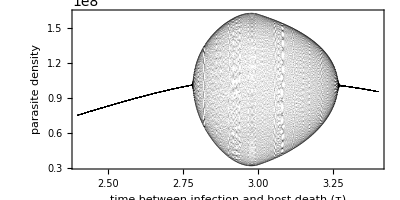

```mathematica
list=Join[list1,list2,list3,list4,list5,list6];
Graphics[{PointSize[0.001],Opacity[0.2],Point[list]},AspectRatio->1/2,Frame->True,FrameLabel->{Style["time between infection and host death (τ)",16,FontFamily->"Helvetica"],Style["parasite density",16,FontFamily->"Helvetica"],Style["T=4, t_l=1",16,FontFamily->"Helvetica"]}]
```

#### code below generate left panel in Figure 3

```mathematica
ClearAll["Global`*"]
```

```mathematica
bpv[T_,tl_,τ_,b_,δ_,a_, d_,σ_,α_,0]:=bpv[T,tl,τ,b,δ,a,d,σ,α,0]=1;
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
bpv[T_,tl_,τ_?NumericQ,b_,δ_,a_, d_,σ_,α_,n_]:=bpv[T,tl,τ,b,δ,a,d,σ,α,n]=
(solv=NDSolve[{
D[s[t], t]==bps[T,tl,τ,b,δ,a,d,σ,α,n-1]* j1[t,tl]-d s[t]-a *s[t]*v1[t],
D[v2[t], t]== a b Exp[-d τ]*s[t-τ]*v1[t-τ]-δ v2[t],
D[v1[t], t]== -δ v1[t],
s[t/;t≤0]==0,v1[t/;t≤0]==bpv[T,tl,τ,b,δ,a,d,σ,α,n-1],v2[t/;t≤0]==0}, 
{v2},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
bpv[T,tl,τ,b,δ,a,d,σ,α,n] =First@Evaluate[v2[T]/.solv]);
bps[T_,tl_,τ_,b_,δ_,a_, d_,σ_,α_,0]:=bps[T,tl,τ,b,δ,a,d,σ,α,0]=10^7;
bps[T_,tl_,τ_?NumericQ,b_,δ_,a_, d_,σ_,α_,n_]:=bps[T,tl,τ,b,δ,a,d,σ,α,n]=
(sols=NDSolve[{
D[s[t], t]==bps[T,tl,τ,b,δ,a,d,σ,α,n-1]* j1[t,tl]-d s[t]-a *s[t]*v1[t],
D[v2[t], t]== a b Exp[-d τ]*s[t-τ]*v1[t-τ]-δ v2[t],
D[v1[t], t]== -δ v1[t],
s[t/;t≤0]==0,v1[t/;t≤0]==bpv[T,tl,τ,b,δ,a,d,σ,α,n-1],v2[t/;t≤0]==0}, 
{s},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
bps[T,tl,τ,b,δ,a,d,σ,α,n]=First@Evaluate[(σ s[T]/(1+α s[T]))/.sols])
list[tt_?NumericQ,tlx_?NumericQ]:=
{bpx=bpv[tt,tlx,tt-tlx,200,2,3.5*10^-7,0.25,500,0.0001,899],bpy=bpv[tt,tlx,tt-tlx,200,2,3.5*10^-7,0.25,500,0.0001,900]}
fun[x_,y_]:=If[x==y,1,0]
rx[k_]:=If[k>100,Round[k,10],k]
```

```mathematica
all=Table[ParallelTable[{xx=bpv[ttx,tlx,ttx-tlx,200,2,3.5*10^-7,0.25,500,0.0001,#]&/@Range[1000];yy={{ttx,tlx,{xx[[999]],xx[[1000]]}}};zz=Map[rx,yy,{3}];
zz[[All,3]]=MapThread[fun[#1,#2]&,{zz[[All,3]][[All,1]],zz[[All,3]][[All,2]]}];
zz},{tlx,0.7,1.5,0.01}],{ttx,3,4,0.01}];
```

```mathematica
allx2=Flatten[all,2];
ally2=Flatten[allx2,1];
```

the kernel crashed periodically in the code above. To correct for this, the table below replaces columns that are erroneously classified as cycling due to numerical errors

```mathematica
allz=Table[{ally2x=Select[ally2,#[[1]]==ttz&];
list=Flatten@Partition[ally2x,2,1];
vvc=Partition[list,6];
tly=Select[vvc,#[[3]]!=#[[6]]&];
tlxx={#2,#5}&@@@tly;
tl11=tlxx[[1,2]];
ally2y=Select[ally2x,#[[2]]>tl11&];
ally2z=Select[ally2x,#[[2]]<=tl11&];
ally2y[[All,3]]=1;
Join[ally2z,ally2y]},{ttz,3,4,0.01}];
```

```mathematica
all3=Table[ParallelTable[{xx=bpv[ttx,tlx,ttx-tlx,200,2,3.5*10^-7,0.25,500,0.0001,#]&/@Range[1000];yy={{ttx,tlx,{xx[[999]],xx[[1000]]}}};zz=Map[rx,yy,{3}];
zz[[All,3]]=MapThread[fun[#1,#2]&,{zz[[All,3]][[All,1]],zz[[All,3]][[All,2]]}];
zz},{tlx,0.7,1.5,0.01}],{ttx,4.01,5,0.01}];
```

```mathematica
allx3=Flatten[all3,2];
ally3=Flatten[allx3,1];
```

```mathematica
xx=Join[ally2,ally3];
sd=StandardDeviation[xx];
{scalex,scaley}=1/Most[sd];
scaledData={scalex,scaley,1} #&/@xx;
```

```mathematica
(*code below smooths plot*)nearest=Nearest[scaledData/. {x_,y_,z_}:>({x,y}->{x,y,z})];
(*local quadratic regression with k neighbours around point (x,y)*)
loess[nearest_,k_][x_,y_]:=Module[{n,d,w,f},n=nearest[{x,y},k];
d=EuclideanDistance[{x,y},Most[#]]&/@n;
d=d/Max[d];
w=(1-d^3)^3;
f=LinearModelFit[n,{u,v,u^2,v^2,u v},{u,v},Weights->w];
f[x,y]]
```

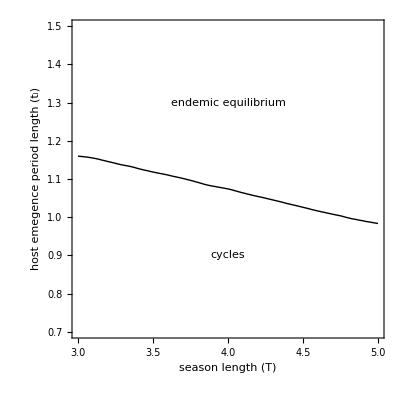

```mathematica
fit=loess[nearest,500];
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}={Min[#],Max[#]}&/@Transpose[xx];
cp=ContourPlot[fit[scalex x,scaley y],{x,xmin,xmax},{y,ymin,ymax},Contours->1,ContourShading->None,FrameLabel->{Style["season length (T)",16,Black],Style["host emegence period length (t_l)",16,Black]},LabelStyle->Directive[Bold,FontFamily->"Helvetica"],Epilog->{Style[Text["cycles",{4,0.9}],16,FontFamily->"Helvetica"],Style[Text["endemic equilibrium",{4,1.3}],16,FontFamily->"Helvetica"]}]
```

#### code below generate left panel in Figure 5

```mathematica
xvv1[τ_,tx_]:=Reap[Do[b=200; a=3.5*10^-7;  δ=2; d=0.25;  tl=1;T=4; σ=500; α=0.0001; 
j1[t_,tl_]:=If[0<t<tl,1/tl,0];
sol=NDSolve[{
D[s1[t], t]==s0 j1[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v2[t], t]== a b Exp[-d τ]*s1[t-τ]*v1[t-τ]-δ v2[t],
D[v1[t], t]== -δ v1[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v10,v2[t/;t≤0]==0}, 
{s1,v1,v2},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
v10 =First@Evaluate[v2[T]/.sol];
s0 = First@Evaluate[σ s1[T]/(1+ α s1[T])/.sol];
Sow[v10,a1];
Sow[s0,a2];
,tx],{a1,a2}];
xvm[τ_,τm_,tx_]:=
Reap@Do[
sol2=NDSolve[{
D[s1[t], t]==s01 j1[t,tl]-d s1[t]-a *s1[t](v1[t]+v1m[t]),
D[v2[t], t]== a b Exp[-d τ]*s1[t-τ]*v1[t-τ]-δ v2[t],
D[v2m[t], t]== a b Exp[-d τm]*s1[t-τm]*v1m[t-τm]-δ v2m[t],
D[v1[t], t]== -δ v1[t],
D[v1m[t], t]==-δ v1m[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v101,v2[t/;t≤0]==0,v1m[t/;t≤0]==v10m,v2m[t/;t≤0]==0}, 
{s1,v1,v2,v1m,v2m},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
v102 =First@Evaluate[v2[T]/.sol2];
v10m =First@Evaluate[v2m[T]/.sol2];
s02 = First@Evaluate[σ s1[T]/(1+ α s1[T])/.sol2];
Sow[v10m];
,10];
```

```mathematica
Clear[v10,v101,s0,s01]
v10=v101=1;s0=s01=10^8;
xx=xvv1[2.8,1500]/.Null->Sequence[];
```

```mathematica
x=Flatten[xx,2][[1]];
y=Flatten[xx,2][[2]];
p=x[[800;;1200]];
h=y[[800;;1200]];
pplotch1=Transpose[{p,h}];
```

finding iterates where mutant invades

```mathematica
Clear[v10,v101,s0,s01,v10m]
v10=1;s0=10^8;v10m=1;
v2mx1=Table[{v=xvv1[2.8,tx]/.Null->Sequence[];
v101=Last[Flatten[v,2][[1]]];
s01=Last[Flatten[v,2][[2]]];Flatten[xvm[2.8,2.81,tx],2][[2;;11]],
Clear[v10,v101,s0,s01,v10m];
v10=v101=1; s0=s01=10^8;v10m=1;},{tx,800,900}] /.Null->Sequence[]
```

```mathematica
Clear[v10,v101,s0,s01,v10m]
v10=1;s0=10^8;v10m=1;
v2mx2=Table[{v=xvv1[2.8,tx]/.Null->Sequence[];
v101=Last[Flatten[v,2][[1]]];
s01=Last[Flatten[v,2][[2]]];Flatten[xvm[2.8,2.81,tx],2][[2;;11]],
Clear[v10,v101,s0,s01,v10m];
v10=v101=1; s0=s01=10^8;v10m=1;},{tx,901,1000}] /.Null->Sequence[]
```

```mathematica
Clear[v10,v101,s0,s01,v10m]
v10=1;s0=10^8;v10m=1;
v2mx3=Table[{v=xvv1[2.8,tx]/.Null->Sequence[];
v101=Last[Flatten[v,2][[1]]];
s01=Last[Flatten[v,2][[2]]];Flatten[xvm[2.8,2.81,tx],2][[2;;11]],
Clear[v10,v101,s0,s01,v10m];
v10=v101=1; s0=s01=10^8;v10m=1;},{tx,1001,1100}] /.Null->Sequence[]
```

```mathematica
Clear[v10,v101,s0,s01,v10m]
v10=1;s0=10^8;v10m=1;
v2mx4=Table[{v=xvv1[2.8,tx]/.Null->Sequence[];
v101=Last[Flatten[v,2][[1]]];
s01=Last[Flatten[v,2][[2]]];Flatten[xvm[2.8,2.81,tx],2][[2;;11]],
Clear[v10,v101,s0,s01,v10m];
v10=v101=1; s0=s01=10^8;v10m=1;},{tx,1101,1200}] /.Null->Sequence[]
```

```mathematica
v2mx=Flatten[Join[v2mx1,v2mx2,v2mx3,v2mx4],1]
```

```mathematica
v2mxx=Flatten[Position[VectorQ[#,#>1&]&/@v2mx,True,{1}]];
```

```mathematica
jlist=(799+#)&/@v2mxx
```

{801,806,811,815,820,829,834,838,843,848,852,857,866,871,875,880,885,889,894,903,908,912,917,922,926,931,940,945,949,954,959,963,968,977,982,986,991,996,1000,1005,1014,1019,1023,1028,1033,1037,1042,1051,1056,1060,1065,1070,1074,1079,1083,1088,1093,1097,1102,1111,1116,1120,1125,1130,1134,1139,1148,1153,1157,1162,1167,1171,1176,1185,1190,1194,1199}

```mathematica
Clear[v10,s0]
v10=1;s0=10^8;
ppm=Table[{v=xvv1[2.8,tx]/.Null->Sequence[];
x=Last[Flatten[v,2][[1]]],
y=Last[Flatten[v,2][[2]]],
Clear[v10,s0];
v10=v101=1; s0=s01=10^8;v10m=1;},{tx,jlist}] /.Null->Sequence[]
```

```mathematica
Clear[v10,s0]
v10=1;s0=10^8;
v=xvv1[2.8,806]/.Null->Sequence[];
x=Last[Flatten[v,2][[1]]];
y=Last[Flatten[v,2][[2]]];
point1={x,y}
```

{7.7316×10^7,3.3075×10^6}

```mathematica
Clear[v10,s0]
v10=1;s0=10^8;
v=xvv1[2.8,807]/.Null->Sequence[];
x=Last[Flatten[v,2][[1]]];
y=Last[Flatten[v,2][[2]]];
point2={x,y}
```

{9.52411×10^7,4.11933×10^6}

```mathematica
Clear[v10,s0]
v10=1;s0=10^8;
v=xvv1[2.8,811]/.Null->Sequence[];
```

```mathematica
xv=Flatten[v,2][[1]];
xs=Flatten[v,2][[2]];
p=xv[[-6;;]];
h=xs[[-6;;]];
arrows=Transpose[{p,h}];
```

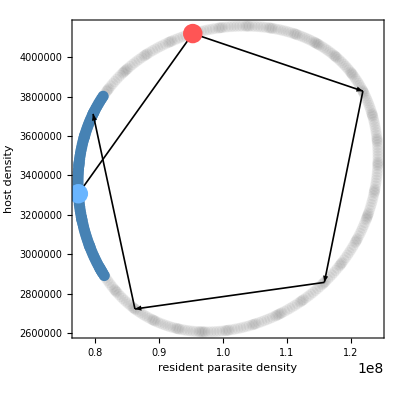

```mathematica
all2=Graphics[{{PointSize[0.02],Opacity[0.05],Point[pplotch1]},{ColorData["HTML"]["SteelBlue"],PointSize[0.02],Point[ppm]},{Thickness[0.003],Arrowheads[{{.04,0.5}}],Arrow/@Partition[arrows,2,1]},{Lighter[ColorData["HTML"]["DodgerBlue"]],PointSize[0.035],Point[point1]},{Lighter[ColorData["HTML"]["Red"]],PointSize[0.035],Point[point2]}},AspectRatio->1,PlotRangePadding->Scaled[.025],Frame->True,FrameStyle->14,FrameLabel->{Style["resident parasite density",20],Style["host density",20],Style["T=4, t_l=1, τ = 2.8",20]}]
```

#### below generates right panel in Figure 5

```mathematica
time=Table[x,{x,806,811}];
pt=Transpose[{time,p}]
```

{{806,7.7316×10^7},{807,9.52411×10^7},{808,1.21899×10^8},{809,1.15858×10^8},{810,8.61816×10^7},{811,7.96205×10^7}}

```mathematica
sdh={806,p[[1]]}
sah={807,p[[2]]}
```

{806,7.7316×10^7}

{807,9.52411×10^7}

```mathematica
discretep=Graphics[{{PointSize[0.02],Opacity[1],Point[pt]},{Black,Thickness[0.003],Line[pt]},{ColorData["HTML"]["DodgerBlue"],PointSize[0.04],Point[sdh]},{ColorData["HTML"]["Red"],PointSize[0.04],Point[sah]}},PlotRangePadding->Scaled[.025],Frame->True,FrameLabel->{Style["",20,FontFamily->"Helvetica"],Style["resident parasite\n   density   ",20,FontFamily->"Helvetica"]},AspectRatio->1/GoldenRatio,PlotRange->{{806,811},{7*10^7,1.3*10^8}},ImageSize->400,FrameTicksStyle->Directive[FontSize->18],FrameTicks->{{{{7*10^7,"7×10^7"},{9*10^7,"9×10^7"},{1.1*10^8,"1.1×10^8"},{1.3*10^8,"1.3×10^8"}},None},{{{806,0},{807,1},{808,2},{809,3},{810,4},{811,5}},None}}];
```

```mathematica
time=Table[x,{x,806,811}];
pth=Transpose[{time,h}]
```

{{806,3.3075×10^6},{807,4.11933×10^6},{808,3.82762×10^6},{809,2.85815×10^6},{810,2.72341×10^6},{811,3.71225×10^6}}

```mathematica
sdhh={806,h[[1]]}
sahh={807,h[[2]]}
```

{806,3.3075×10^6}

{807,4.11933×10^6}

```mathematica
discreteh=Graphics[{{PointSize[0.02],Opacity[1],Point[pth]},{Black,Thickness[0.003],Line[pth]},{ColorData["HTML"]["DodgerBlue"],PointSize[0.04],Point[sdhh]},{ColorData["HTML"]["Red"],PointSize[0.04],Point[sahh]}},PlotRangePadding->Scaled[.025],Frame->True,FrameLabel->{Style["",20,FontFamily->"Helvetica"],Style["host density\n  ",20,FontFamily->"Helvetica"],Style["host and parasite dynamics",24,FontFamily->"Helvetica"]},AspectRatio->1/GoldenRatio,PlotRange->{{806,811},{2.5*10^6,4.5*10^6}},ImageSize->400,FrameTicksStyle->Directive[FontSize->18],FrameTicks->{{{{2.5*10^6,"2.5×10^6"},{3.5*10^6,"3.5×10^6"},{4.5*10^6,"4.5×10^6"}},None},{{{806,0},{807,1},{808,2},{809,3},{810,4},{811,5}},None}}];
```

```mathematica
Clear[v10,v101,s0,s01,v10m]
v10=1;s0=10^8;v10m=1;
v=xvv1[2.8,806]/.Null->Sequence[];
v101=Last[Flatten[v,2][[1]]];
s01=Last[Flatten[v,2][[2]]];
v2mxpt1=Flatten[xvm[2.8,2.81,806],2][[2;;11]]
```

{1.24318,1.6072,1.5448,1.16178,1.08369,1.47484,1.72503,1.47365,1.12275,1.25719}

```mathematica
time=Table[x,{x,1,6}];
v2mpt1=Transpose[{time,v2mxpt1[[;;6]]}]
```

{{1,1.24318},{2,1.6072},{3,1.5448},{4,1.16178},{5,1.08369},{6,1.47484}}

```mathematica
discretem1=Graphics[{{PointSize[0.02],Opacity[1],Point[v2mpt1]},{ColorData["HTML"]["DodgerBlue"],Thickness[0.003],Line[v2mpt1]},{ColorData["HTML"]["DodgerBlue"],PointSize[0.04],Point[{0,1}]}},PlotRangePadding->Scaled[.025],Frame->True,FrameLabel->{Style[" ",20],Style["mutant parasite density \n    ",20],Style["invading mutant\n parasite dynamics",24]},AspectRatio->1/GoldenRatio,PlotRange->{{0,5},{0.95,2}},ImageSize->400,FrameTicksStyle->Directive[FontSize->18]];
```

```mathematica
Clear[v10,v101,s0,s01,v10m]
v10=1;s0=10^8;v10m=1;
v=xvv1[2.8,807]/.Null->Sequence[];
v101=Last[Flatten[v,2][[1]]];
s01=Last[Flatten[v,2][[2]]];
v2mxpt2=Flatten[xvm[2.8,2.81,807],2][[2;;11]]
```

{1.29281,1.24262,0.934521,0.87171,1.18635,1.3876,1.18539,0.903131,1.01127,1.36678}

```mathematica
time=Table[x,{x,1,2}];
v2mpt2=Transpose[{time,v2mxpt2[[;;2]]}]
```

{{1,1.29281},{2,1.24262}}

```mathematica
time=Table[x,{x,1,2}];
v2mpt2={{1,1},{2,1.2928149464572882},{3,1.2426178434760824}}
```

{{1,1},{2,1.29281},{3,1.24262}}

```mathematica
time=Table[x,{x,1,2}];
v2mpt2l={{1,1},{2,1.2928149464572882},{3,1.2426178434760824},{4,0.93}}
```

{{1,1},{2,1.29281},{3,1.24262},{4,0.93}}

```mathematica
discretem2=Graphics[{{PointSize[0.02],Opacity[1],Point[v2mpt1]},{ColorData["HTML"]["DodgerBlue"],Thickness[0.003],Line[v2mpt1]},{ColorData["HTML"]["DodgerBlue"],PointSize[0.04],Point[{0,1}]},{PointSize[0.02],Opacity[1],Point[v2mpt2]},{ColorData["HTML"]["Red"],Thickness[0.003],Line[v2mpt2l]},{ColorData["HTML"]["Red"],PointSize[0.04],Point[{1,1}]}},PlotRangePadding->Scaled[.025],Frame->True,FrameLabel->{Style["season ",20],Style["mutant parasite\n   density   \n",20]},AspectRatio->1/GoldenRatio,PlotRange->{{0,5},{0.95,2}},ImageSize->400,FrameTicksStyle->Directive[FontSize->18],FrameTicks->{{{{1,"1.0"},{1.2,"1.2"},{1.4,"1.4"},{1.6,"1.6"},{1.8,"1.8"},{2,"2.0"}},None},{{{0,0},{1,1},{2,2},{3,3},{4,4},{5,5}},None}}];
```

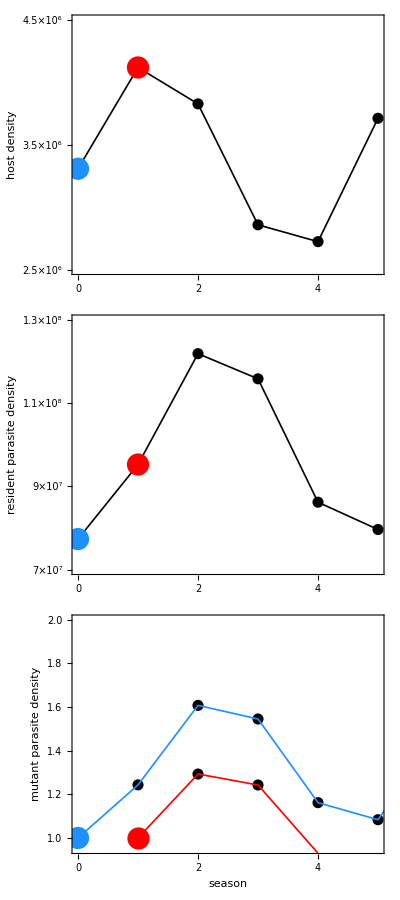

```mathematica
n2=Grid[{{discreteh},{discretep},{discretem2}},Spacings->0]
```